```mathematica
Quiet@Remove@"`*";ClearAll@"`*";
On[Assert]
SetDirectory[NotebookDirectory[]];

Row@{"Suffix: ",suffix="hT"}
mcData=Import[StringJoin["mc-",suffix,".json"], "RawJSON"];
a1Data=Import[StringJoin["a1-",suffix,".json"], "RawJSON"];
a2Data=Import[StringJoin["a2-",suffix,".json"], "RawJSON"];
```

Suffix: hT

Sample sizes: 10000

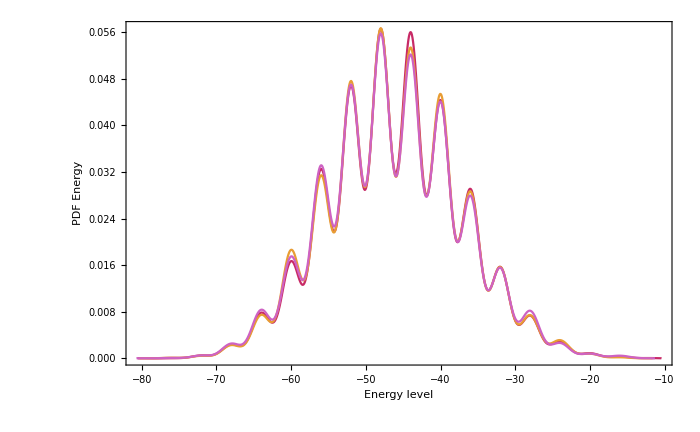

```mathematica
{engyMc,engyA1,engyA2} =#["energy_sample"] &/@{mcData,a1Data,a2Data};


Row@{"Sample sizes: ",sampleSize=Length[engyMc]}
Assert@And[
sampleSize==Length[engyA1],
sampleSize==Length[engyA2]
]

colors = Table[ColorData[54][i],{i,6}];
baseStyle = Directive[Black, FontFamily->"Arial", FontSize->16];
frameStyle = Append[baseStyle, Thickness@0.003];

mc = SmoothHistogram[engyMc,Automatic, "PDF", PlotRange->All,PlotStyle-> colors[[1]],Axes->False];
a1 = SmoothHistogram[engyA1,Automatic, "PDF", PlotRange->All,PlotStyle-> colors[[2]],Axes->False];
a2 = SmoothHistogram[engyA2,Automatic, "PDF", PlotRange->All,PlotStyle-> colors[[3]],Axes->False];
Show[
{mc, a1, a2},
Epilog->{
Inset[Framed[
SwatchLegend[
Directive[EdgeForm@None,FaceForm@#]&/@colors,
{"MC","A1","A2"},
LegendLayout->"Row",LabelStyle->baseStyle
],FrameStyle->Append[baseStyle,Thickness@1],RoundingRadius->5
],Scaled@{0.7,0.9}]
},
Frame->{{True,True},{True,True}},
FrameStyle->{{Append[baseStyle,Thickness@0.004],Append[baseStyle,Thickness@0.004]},{Append[baseStyle,Thickness@0.004],Append[baseStyle,Thickness@0.004]}},
FrameLabel->{{"PDF Energy",""},{"Energy level",""}}, 
ImageSize->700
]
```

```mathematica
PearsonChiSquareTest[engyA1, engyMc]
PearsonChiSquareTest[engyA2, engyMc]
```

0.780538

0.722462